```mathematica
g=9.81;m=X;
r=0.4;l=2;h=1;mA=mB=10;θ=mA/2 r^2;M=1000;
```

```mathematica
eq1=m a==-KAx-KBx;
eq2=0==-KAy-KBy-m g;
eq3=0==-KAx h-KBx h+KAy l-KBy l;
eq4=mA a==KAx+SA;
eq5=0==KAy-g mA+NA;
eq6=θ ε==SA r-M;
eq7=mB a==KBx+SB;
eq8=0==KBy-g mB+NB;
eq9=θ ε==SB r;
eq10=a==-ε r;
```

```mathematica
Solve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10},{a,ε,KAx,KAy,SA,NA,KBx,KBy,SB,NB}][[1]]//Chop//Column
```

a→2500./(30.+1. X)
ε→-6250./(30.+1. X)
KAx→-(2500. (15.+1. X))/(30.+1. X)
KAy→-(4.905 (157.421 X+1. X^2))/(30.+1. X)
SA→(2500. (25.+1. X))/(30.+1. X)
NA→(4.905 (600.+177.421 X+1. X^2))/(30.+1. X)
KBx→37500./(30.+1. X)
KBy→-(4.905 (-97.421 X+1. X^2))/(30.+1. X)
SB→-12500./(30.+1. X)
NB→(4.905 (600.-77.421 X+1. X^2))/(30.+1. X)

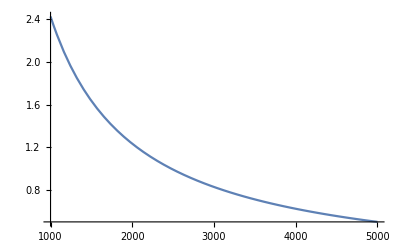

```mathematica
Plot[2500/(30+X),{X,1000,5000},PlotRange->Full]
```

```mathematica
{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10}//Column;
```

```mathematica
Coefficients=CoefficientArrays[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10},{a,ε,KAx,KAy,SA,NA,KBx,KBy,SB,NB}]
```

{SparseArray[…],SparseArray[…]}

```mathematica
b=-Coefficients[[1]];A=Coefficients[[2]];
```

```mathematica
Inverse[A].b//FullSimplify//Chop//MatrixForm
```

(2500./(30.+1. X)
-6250./(30.+1. X)
-2500.+37500./(30.+1. X)
-(772.15 X)/(30.+1. X)-(4.905 X^2)/(30.+1. X)
2500.-12500./(30.+1. X)
2943./(30.+1. X)+(X (870.25+4.905 X))/(30.+1. X)
37500./(30.+1. X)
(477.85 X)/(30.+1. X)-(4.905 X^2)/(30.+1. X)
-12500./(30.+1. X)
2943./(30.+1. X)+(X (-379.75+4.905 X))/(30.+1. X))